### Basic Examples (3)

Perform persistent homology on random data:

```mathematica
SeedRandom[314];data = RandomReal[{0,1},{10,3} ];
ph=[data]
```

PersistentHomologyObject[…]

Query the output for the barcode:

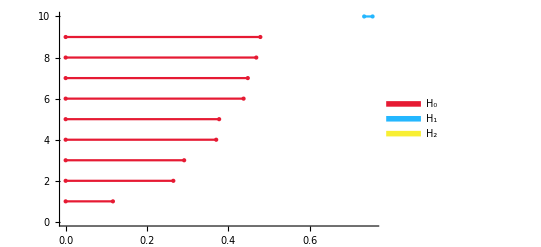

```mathematica
ph["Barcode"]
```

Visualize the MeshRegion for the H_1 generator found:

```mathematica
ph["GeneratorMeshes"][[10]]
```

-Graphics3D-

### Scope (2)

#### Dimensionality (2)

PersistentHomology can be performed for data of any dimension:

```mathematica
data=RandomReal[{0,1},{10,42}];
```

```mathematica
[data]
```

PersistentHomologyObject[…]

Evaluate the persistent homology of data with dimension 1000:

```mathematica
data=RandomReal[{0,1},{10,1000}];
```

```mathematica
[data]
```

PersistentHomologyObject[…]

### Options (3)

#### Distance (2)

The maximum distance used in computations can be specified:

```mathematica
data=RandomReal[{0,1},{10,3}];
```

```mathematica
[data,"Distance"->0.75]
```

PersistentHomologyObject[…]

This will sometimes speed up computation times:

```mathematica
AbsoluteTiming[[data,"Distance"->0.75]]
```

{7.64044,PersistentHomologyObject[…]}

```mathematica
AbsoluteTiming[[data]]
```

{7.52512,PersistentHomologyObject[…]}

#### Modulus (1)

The finite field chosen for computations can be specified:

```mathematica
data=RandomReal[{0,1},{10,3}];
```

```mathematica
[data,"Modulus"->7]
```

PersistentHomologyObject[<|Points -> {{0.540558, 0.208324, 0.0814161}, {0.00129297, 0.446641, 0.894455}, {0.164448, 0.609031, 0.0627587}, {0.115234, 0.441508, 0.799684}, {0.41501, 0.426921, 0.87408}, {0.471, 0.415582, 0.295995}, {0.457074, 0.890579, 0.952611}, {0.552771, 0.653242, 0.356828}, {0.279893, 0.462175, 0.945655}, {0.990844, 0.0672289, 0.938108}}, <<7>>, Edges -> <<1>>|>]

### Properties and Relations (1)

PersistentHomology is invariant under isometries:

```mathematica
data=SpherePoints[10];
```

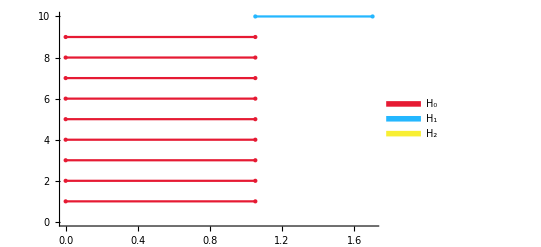

```mathematica
[data]["Barcode"]
```

```mathematica
[({0,0,1}+#1&)/@SpherePoints[10]]["Barcode"]
```

-Graphics-

```mathematica
[RotationTransform[π/4,{1,1,1}][data]]["Barcode"]
```

-Graphics-

### Possible Issues (1)

PersistentHomology computation times grow quickly in the number of data points:

```mathematica
data=RandomReal[{0,1},{20,3}];
AbsoluteTiming[[data⟦1;;5⟧]]
```

{6.95572,PersistentHomologyObject[…]}

```mathematica
AbsoluteTiming[[data⟦1;;10⟧]]
```

{7.33262,PersistentHomologyObject[…]}

```mathematica
AbsoluteTiming[[data⟦1;;15⟧]]
```

{22.7267,PersistentHomologyObject[<|Points -> {{0.407456, 0.324138, 0.252778}, {0.966994, 0.613372, 0.815813}, {0.336938, 0.54071, 0.372096}, {0.028556, 0.764784, 0.736238}, {0.736004, 0.350236, 0.99665}, {0.815259, 0.247619, 0.242471}, {0.168575, 0.126054, 0.407273}, <<5>>, {0.0485355, 0.101531, 0.487586}, {0.164593, 0.391053, 0.7659}, {0.0732095, 0.775192, 0.537681}}, <<8>>|>]}

```mathematica
AbsoluteTiming[[data⟦1;;20⟧]]
```

{225.966,PersistentHomologyObject[<|Points -> {{0.407456, 0.324138, 0.252778}, {0.966994, 0.613372, 0.815813}, {0.336938, 0.54071, 0.372096}, {0.028556, 0.764784, 0.736238}, {0.736004, 0.350236, 0.99665}, {0.815259, 0.247619, 0.242471}, {0.168575, 0.126054, 0.407273}, <<10>>, {0.248729, 0.295658, 0.758131}, {0.398079, 0.758276, 0.725927}, {0.348824, 0.452581, 0.362966}}, <<8>>|>]}

### Neat Examples (1)

Draw some data in ℝ^2 and perform PersistentHomology on it:

```mathematica
DynamicModule[{data={},phom=Graphics[{}]},
Column[{
Button["Compute",phom=[data]["Barcode"]],
Row@{ClickPane[Framed@Dynamic[ListPlot[data,PlotRange->{ {-1,1},{-1,1} },PlotStyle->PointSize[Large],ImageSize->250,PlotLabel->Length[data]],],AppendTo[data,#]&],Dynamic[Show[phom,ImageSize->250]]}
},Alignment->Left
]]
```

-Graphics-